0.0369495

-0.00585059

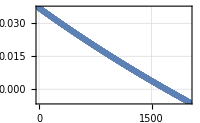

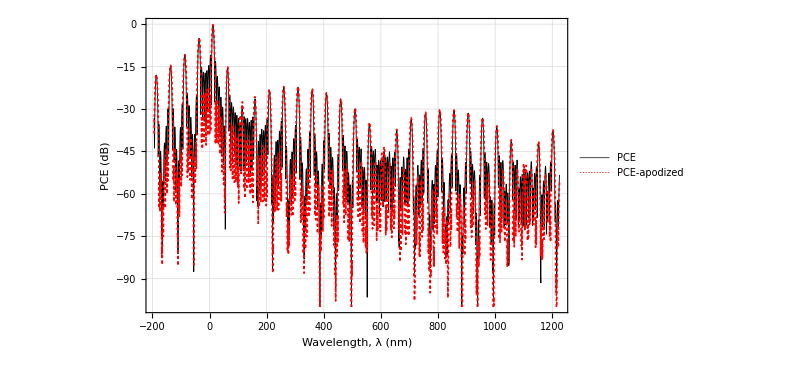

```mathematica
n3=2.2119;
n1=2.1386;
n=Sqrt[n3*n1];
Subscript[Δ, ngr]=0.08;

period=21;
lc=(179+3/4)*period;
lpa=(20)*period;
lpb=(20+2/4)*period;
L=lc*8+lpa*4+lpb*3;

lambda0=period*(n3-n1);
lambdaj=lambda0-0.0016;

npoints=2000;

S=Pi/(2*3.02*10^4);
PCE=Table[{0},{i,1,npoints}];
PCEa=Table[{0},{i,1,npoints}];
dvec=Table[{0},{i,1,npoints}];

For[k=1,k<=npoints,k++,lambda=1.37+0.0001*k;
delta=2*Pi*(n3-n1)*(1/lambda-1/lambda0);
deltaj=2*Pi*Subscript[Δ, ngr]*(1/lambdaj-1/lambda0);
d=delta/2;
b1=2*Pi/lambda*n1;
b2=2*Pi/lambda*n3;
K1=S*Cos[deltaj*1/16*L];
K1a=S*Cos[deltaj*1/16*L]*(1+0.5*Cos[2*Pi*(1/16-0.5)]);
ac1=Cos[Sqrt[K1^2+d^2]*lc]+I*d/Sqrt[K1^2+d^2]*Sin[Sqrt[K1^2+d^2]*lc];
bc1=-I*K1/Sqrt[K1^2+d^2]*Sin[Sqrt[K1^2+d^2]*lc];
ac1a=Cos[Sqrt[K1a^2+d^2]*lc]+I*d/Sqrt[K1a^2+d^2]*Sin[Sqrt[K1a^2+d^2]*lc];
bc1a=-I*K1a/Sqrt[K1a^2+d^2]*Sin[Sqrt[K1a^2+d^2]*lc];
MC1={{ac1*Exp[-I*(b1+d)*lc],bc1*Exp[-I*(b1+d)*lc]},{-Conjugate[bc1]*Exp[-I*(b2-d)*lc],Conjugate[ac1]*Exp[-I*(b2-d)*lc]}};
MC1a={{ac1a*Exp[-I*(b1+d)*lc],bc1a*Exp[-I*(b1+d)*lc]},{-Conjugate[bc1a]*Exp[-I*(b2-d)*lc],Conjugate[ac1a]*Exp[-I*(b2-d)*lc]}};
MP2={{Exp[-I*b1*lpa],0},{0,Exp[-I*b2*lpa]}};
K2=S*Sin[deltaj*3/16*L];
K2a=S*Sin[deltaj*3/16*L]*(1+0.5*Cos[2*Pi*(3/16-0.5)]);
ac2=Cos[Sqrt[K2^2+d^2]*lc]+I*d/Sqrt[K2^2+d^2]*Sin[Sqrt[K2^2+d^2]*lc];
bc2=-I*K2/Sqrt[K2^2+d^2]*Sin[Sqrt[K2^2+d^2]*lc];
ac2a=Cos[Sqrt[K2a^2+d^2]*lc]+I*d/Sqrt[K2a^2+d^2]*Sin[Sqrt[K2a^2+d^2]*lc];
bc2a=-I*K2a/Sqrt[K2a^2+d^2]*Sin[Sqrt[K2a^2+d^2]*lc];
MC2={{ac2*Exp[-I*(b1+d)*lc],bc2*Exp[-I*(b1+d)*lc]},{-Conjugate[bc2]*Exp[-I*(b2-d)*lc],Conjugate[ac2]*Exp[-I*(b2-d)*lc]}};
MC2a={{ac2a*Exp[-I*(b1+d)*lc],bc2a*Exp[-I*(b1+d)*lc]},{-Conjugate[bc2a]*Exp[-I*(b2-d)*lc],Conjugate[ac2a]*Exp[-I*(b2-d)*lc]}};
T2=MC2.MP2;
T2a=MC2a.MP2;
MP3={{Exp[-I*b1*lpb],0},{0,Exp[-I*b2*lpb]}};
K3=S*Cos[deltaj*5/16*L];
K3a=S*Cos[deltaj*5/16*L]*(1+0.5*Cos[2*Pi*(5/16-0.5)]);
ac3=Cos[Sqrt[K3^2+d^2]*lc]+I*d/Sqrt[K3^2+d^2]*Sin[Sqrt[K3^2+d^2]*lc];
bc3=-I*K3/Sqrt[K3^2+d^2]*Sin[Sqrt[K3^2+d^2]*lc];
ac3a=Cos[Sqrt[K3a^2+d^2]*lc]+I*d/Sqrt[K3a^2+d^2]*Sin[Sqrt[K3a^2+d^2]*lc];
bc3a=-I*K3a/Sqrt[K3a^2+d^2]*Sin[Sqrt[K3a^2+d^2]*lc];
MC3={{ac3*Exp[-I*(b1+d)*lc],bc3*Exp[-I*(b1+d)*lc]},{-Conjugate[bc3]*Exp[-I*(b2-d)*lc],Conjugate[ac3]*Exp[-I*(b2-d)*lc]}};
MC3a={{ac3a*Exp[-I*(b1+d)*lc],bc3a*Exp[-I*(b1+d)*lc]},{-Conjugate[bc3a]*Exp[-I*(b2-d)*lc],Conjugate[ac3a]*Exp[-I*(b2-d)*lc]}};
T3=MC3.MP3;
T3a=MC3a.MP3;
MP4={{Exp[-I*b1*lpa],0},{0,Exp[-I*b2*lpa]}};
K4=S*Sin[deltaj*7/16*L];
K4a=S*Sin[deltaj*7/16*L]*(1+0.5*Cos[2*Pi*(7/16-0.5)]);
ac4=Cos[Sqrt[K4^2+d^2]*lc]+I*d/Sqrt[K4^2+d^2]*Sin[Sqrt[K4^2+d^2]*lc];
bc4=-I*K4/Sqrt[K4^2+d^2]*Sin[Sqrt[K4^2+d^2]*lc];
ac4a=Cos[Sqrt[K4a^2+d^2]*lc]+I*d/Sqrt[K4a^2+d^2]*Sin[Sqrt[K4a^2+d^2]*lc];
bc4a=-I*K4a/Sqrt[K4a^2+d^2]*Sin[Sqrt[K4a^2+d^2]*lc];
MC4={{ac4*Exp[-I*(b1+d)*lc],bc4*Exp[-I*(b1+d)*lc]},{-Conjugate[bc4]*Exp[-I*(b2-d)*lc],Conjugate[ac4]*Exp[-I*(b2-d)*lc]}};
MC4a={{ac4a*Exp[-I*(b1+d)*lc],bc4a*Exp[-I*(b1+d)*lc]},{-Conjugate[bc4a]*Exp[-I*(b2-d)*lc],Conjugate[ac4a]*Exp[-I*(b2-d)*lc]}};
T4=MC4.MP4;
T4a=MC4a.MP4;
MP5={{Exp[-I*b1*lpb],0},{0,Exp[-I*b2*lpb]}};
K5=S*Cos[deltaj*9/16*L];
K5a=S*Cos[deltaj*9/16*L]*(1+0.5*Cos[2*Pi*(9/16-0.5)]);
ac5=Cos[Sqrt[K5^2+d^2]*lc]+I*d/Sqrt[K5^2+d^2]*Sin[Sqrt[K5^2+d^2]*lc];
bc5=-I*K5/Sqrt[K5^2+d^2]*Sin[Sqrt[K5^2+d^2]*lc];
ac5a=Cos[Sqrt[K5a^2+d^2]*lc]+I*d/Sqrt[K5a^2+d^2]*Sin[Sqrt[K5a^2+d^2]*lc];
bc5a=-I*K5a/Sqrt[K5a^2+d^2]*Sin[Sqrt[K5a^2+d^2]*lc];
MC5={{ac5*Exp[-I*(b1+d)*lc],bc5*Exp[-I*(b1+d)*lc]},{-Conjugate[bc5]*Exp[-I*(b2-d)*lc],Conjugate[ac5]*Exp[-I*(b2-d)*lc]}};
MC5a={{ac5a*Exp[-I*(b1+d)*lc],bc5a*Exp[-I*(b1+d)*lc]},{-Conjugate[bc5a]*Exp[-I*(b2-d)*lc],Conjugate[ac5a]*Exp[-I*(b2-d)*lc]}};
T5=MC5.MP5;
T5a=MC5a.MP5;
MP6={{Exp[-I*b1*lpa],0},{0,Exp[-I*b2*lpa]}};
K6=S*Sin[deltaj*11/16*L];
K6a=S*Sin[deltaj*11/16*L]*(1+0.5*Cos[2*Pi*(11/16-0.5)]);
ac6=Cos[Sqrt[K6^2+d^2]*lc]+I*d/Sqrt[K6^2+d^2]*Sin[Sqrt[K6^2+d^2]*lc];
bc6=-I*K6/Sqrt[K6^2+d^2]*Sin[Sqrt[K6^2+d^2]*lc];
ac6a=Cos[Sqrt[K6a^2+d^2]*lc]+I*d/Sqrt[K6a^2+d^2]*Sin[Sqrt[K6a^2+d^2]*lc];
bc6a=-I*K6a/Sqrt[K6a^2+d^2]*Sin[Sqrt[K6a^2+d^2]*lc];
MC6={{ac6*Exp[-I*(b1+d)*lc],bc6*Exp[-I*(b1+d)*lc]},{-Conjugate[bc6]*Exp[-I*(b2-d)*lc],Conjugate[ac6]*Exp[-I*(b2-d)*lc]}};
MC6a={{ac6a*Exp[-I*(b1+d)*lc],bc6a*Exp[-I*(b1+d)*lc]},{-Conjugate[bc6a]*Exp[-I*(b2-d)*lc],Conjugate[ac6a]*Exp[-I*(b2-d)*lc]}};
T6=MC6.MP6;
T6a=MC6a.MP6;
MP7={{Exp[-I*b1*lpb],0},{0,Exp[-I*b2*lpb]}};
K7=S*Cos[deltaj*13/16*L];
K7a=S*Cos[deltaj*13/16*L]*(1+0.5*Cos[2*Pi*(13/16-0.5)]);
ac7=Cos[Sqrt[K7^2+d^2]*lc]+I*d/Sqrt[K7^2+d^2]*Sin[Sqrt[K7^2+d^2]*lc];
bc7=-I*K7/Sqrt[K7^2+d^2]*Sin[Sqrt[K7^2+d^2]*lc];
ac7a=Cos[Sqrt[K7a^2+d^2]*lc]+I*d/Sqrt[K7a^2+d^2]*Sin[Sqrt[K7a^2+d^2]*lc];
bc7a=-I*K7a/Sqrt[K7a^2+d^2]*Sin[Sqrt[K7a^2+d^2]*lc];
MC7={{ac7*Exp[-I*(b1+d)*lc],bc7*Exp[-I*(b1+d)*lc]},{-Conjugate[bc7]*Exp[-I*(b2-d)*lc],Conjugate[ac7]*Exp[-I*(b2-d)*lc]}};
MC7a={{ac7a*Exp[-I*(b1+d)*lc],bc7a*Exp[-I*(b1+d)*lc]},{-Conjugate[bc7a]*Exp[-I*(b2-d)*lc],Conjugate[ac7a]*Exp[-I*(b2-d)*lc]}};
T7=MC7.MP7;
T7a=MC7a.MP7;
MP8={{Exp[-I*b1*lpa],0},{0,Exp[-I*b2*lpa]}};
K8=S*Sin[deltaj*15/16*L];
K8a=S*Sin[deltaj*15/16*L]*(1+0.5*Cos[2*Pi*(15/16-0.5)]);
ac8=Cos[Sqrt[K8^2+d^2]*lc]+I*d/Sqrt[K8^2+d^2]*Sin[Sqrt[K8^2+d^2]*lc];
bc8=-I*K8/Sqrt[K8^2+d^2]*Sin[Sqrt[K8^2+d^2]*lc];
ac8a=Cos[Sqrt[K8a^2+d^2]*lc]+I*d/Sqrt[K8a^2+d^2]*Sin[Sqrt[K8a^2+d^2]*lc];
bc8a=-I*K8a/Sqrt[K8a^2+d^2]*Sin[Sqrt[K8a^2+d^2]*lc];
MC8={{ac8*Exp[-I*(b1+d)*lc],bc8*Exp[-I*(b1+d)*lc]},{-Conjugate[bc8]*Exp[-I*(b2-d)*lc],Conjugate[ac8]*Exp[-I*(b2-d)*lc]}};
MC8a={{ac8a*Exp[-I*(b1+d)*lc],bc8a*Exp[-I*(b1+d)*lc]},{-Conjugate[bc8a]*Exp[-I*(b2-d)*lc],Conjugate[ac8a]*Exp[-I*(b2-d)*lc]}};
T8=MC8.MP8;
T8a=MC8a.MP8;
Cm=T8.T7.T6.T5.T4.T3.T2.MC1;
PCE[[k]]=10*Log10[(Abs[Cm[[1]][[2]]])^2];
Cma=T8a.T7a.T6a.T5a.T4a.T3a.T2a.MC1a;
PCEa[[k]]=10*Log10[(Abs[Cma[[1]][[2]]])^2];
dvec[[k]]=delta;
]
dvec[[1]]
dvec[[2000]]
ListLinePlot[dvec,Joined->True,PlotMarkers->{Blue,1},GridLines->Automatic ,Frame->True,FrameLabel->{Style["k",Black,Bold],Style["dvec",Black,Bold]},ImageSize->200]
P1=ListLinePlot[Table[{dvec[[m]]*L,PCE[[m]]},{m,1,npoints}],PlotRange->{Automatic,{-100,0}},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{{Black,Thickness[0.001]}},PlotLegends->{"PCE"},FrameLabel->{Style["Wavelength, λ (nm)",Black,Bold],Style["PCE (dB)",Black,Bold]},ImageSize->600];
P2=ListLinePlot[Table[{dvec[[m]]*L,PCEa[[m]]},{m,1,npoints}],PlotRange->{Automatic,{-100,0}},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{{Red,Dashing[Tiny],Thickness[0.002]}},PlotLegends->{"PCE-apodized"}];
Show[P1,P2]
```